Implementing D_HI - M_HI relation
The relation between total HI mass and D_HI (defined as the HI diameter where the surface density is 1 solar mass / pc^2) as given by Wang 2016 is 
log_10(D_HI) =0.506 log_10(M_HI)-3.293
Thus we have 2 unknowns in the surface density formula
Σ(r) = Σ_0 Exp(-r/rs)
namely Σ_0 and rs, and two constraints: 
M_HI=∫_0^∞ 2π r Σ_0 Exp(-r/rs)ⅆr
1 solmass / pc^2 = Σ_0 Exp[-(D_HI/2)/rs]
The above integral is analytic,

```mathematica
∫_0^∞ 2 π r Subscript[Σ, 0] Exp[-r/rs]ⅆr
```

ConditionalExpression[2 π rs^2 Σ_0,Re[rs]>0]

Such that M_HI=2π Σ_0 rs^2. Given two equations and two unknowns, we can solve

```mathematica
Solve[MHI/(2 π  rs^2)Exp[(-(DHI/2))/rs]==x,rs]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rs→-DHI/(4 ProductLog[-1/2 √(π/2) √((DHI^2 x)/MHI)])},{rs→-DHI/(4 ProductLog[1/2 √(π/2) √((DHI^2 x)/MHI)])}}

Move the negative exponential over 
MHI/(2 π  rs^2)==x Exp[(DHI/2)/rs]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-DHI/(√(2 π) √(MHI Σ))) Σ==x,Σ]

This gives too much output to be useful

```mathematica
Reduce[MHI/(2 π  rs^2)Exp[(-(DHI/2))/rs]==x,rs,Reals]
```

```mathematica
ProductLog[-0.5*Sqrt[π/2] * Sqrt[0.5^2/10^6]]
```

-0.000313427

```mathematica
D[-DHI/(4 ProductLog[-1/2 √(DHI^2/MHI) √(π/2)]),MHI]
```

-DHI/(8 MHI ProductLog[-1/2 √(DHI^2/MHI) √(π/2)] (1+ProductLog[-1/2 √(DHI^2/MHI) √(π/2)]))

```mathematica
D[-DHI/(4 ProductLog[-1/2 √(DHI^2/MHI) √(π/2)]),DHI]
```

-1/(4 ProductLog[-1/2 √(DHI^2/MHI) √(π/2)])+1/(4 ProductLog[-1/2 √(DHI^2/MHI) √(π/2)] (1+ProductLog[-1/2 √(DHI^2/MHI) √(π/2)]))

```mathematica
ProductLog[-0.4]
```

-0.94409+0.407268 ⅈ

```mathematica
ProductLog[0,-0.4]
```

-0.94409+0.407268 ⅈ

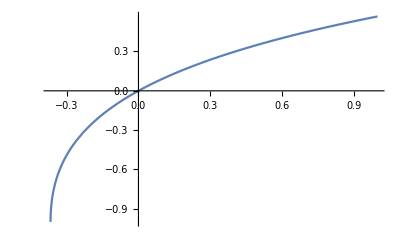

```mathematica
Plot[ProductLog[x],{x,-1/E,1}]
```

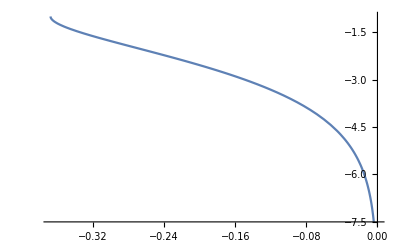

```mathematica
Plot[ProductLog[-1,x],{x,-1/E,0}]
```

```mathematica
ProductLog[-2/E]
```

ProductLog[-2/ⅇ]

```mathematica
N[ProductLog[-1/ⅇ-0.1]]
```

-0.838834+0.684252 ⅈ

```mathematica
Solve[D[1 - x * Exp[-DD/(2*Sqrt[M/(2π x)])],x]==0,x]
```

{{x→(8 M)/(DD^2 π)}}

```mathematica
Solve[1 - x * Exp[-DD/(2*Sqrt[M/(2π x)])]==0,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-ⅇ^(-(DD √(π/2))/(√(M/x))) x==0,x,Reals]

This just reduces to the same thing as solving for rs, doesn’t get us around the Lambert W problem

```mathematica
Solve[1/Sqrt[x] Log[1/x]==-D/(2Sqrt[M/(2π)]),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(8 M ProductLog[-1/2 √(D^2/M) √(π/2)]^2)/(D^2 π)},{x→(8 M ProductLog[1/2 √(D^2/M) √(π/2)]^2)/(D^2 π)}}

What if we change the definition of the HI mass to be the total mass enclosed within DHI?

```mathematica
∫_0^(DHI/2) 2 π r Subscript[Σ, 0] Exp[-r/rs]ⅆr
```

2 π rs (rs-1/2 ⅇ^(-DHI/(2 rs)) (DHI+2 rs)) Σ_0

```mathematica
Solve[MHI/(2 π rs (rs-1/2 ⅇ^(-DHI/(2 rs)) (DHI+2 rs))) Exp[(-(DHI/2))/rs]==1,rs]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ⅇ^(-DHI/(2 rs)) MHI)/(2 π rs (rs-1/2 ⅇ^(-DHI/(2 rs)) (DHI+2 rs)))==1,rs]

Not helpful